Part 1 - Derivation of slope 'a' ((β̂)_1) and intercept 'b' ((β̂)_0):

(1) Linear relationship between stopping voltage and frequency of incident light
	V(ν) = aν + b can be modeled with the same equation (Ŷ)_k = (β̂)_0+(β̂)_1 X_k where (Ŷ)_k is the
	predicted response variable (V(ν)) and X_k is the kth explanatory variable (ν).

(2) The sum of squared errors, also known as the mean squared error, is
	the sum of the difference between all response values in the data set (Y_k) and 
	predicted response values ((Ŷ)_k) and is modeled by the equation SSE = ∑_(k = 1)^N (Y_k-(Ŷ)_k)^2 
	for the k^th term in a data set with N terms.

(3) Substituting the definition of (Ŷ)_k into SSE yields an equation which,
	once differentiated with respect to (β̂)_1 and (β̂)_0 and set equal to 0, may be solved
	simultaneously to yield the minimum values of (β̂)_1 and (β̂)_0 to minimize the 'distance' 
	between the prediction 'line' and values of Y_k: SSE = ∑_(k = 1)^N (Y_k-((β̂)_0 + (β̂)_1X_k))^2

(4)  (∂SSE)/(∂SubscriptBox[OverscriptBox[β, ^], 0])∑_(k = 1)^N (Y_k-((β̂)_0 + (β̂)_1X_k))^2 = ∑_(k = 1)^N -2 (-(β̂)_0-(β̂)_1 X_k+Y_k)	and (∂SSE)/(∂SubscriptBox[OverscriptBox[β, ^], 1])∑_(k = 1)^N (Y_k-((β̂)_0 + (β̂)_1X_k))^2 = ∑_(k = 1)^N -2 X_k (-(β̂)_0-(β̂)_1 X_k+Y_k)

(5) The solution for (β̂)_0 N = -(β̂)_1 X_k+Y_k for N values in the  
	data is equivalent to (B̂)_0 = Ȳ - (B̂)_1X̄ where Ȳ and X̄ are the average of the X and 
	Y values in the data.

(6) Substituting (B̂)_0 in terms of (B̂)_1 into (∂SSE)/(∂SubscriptBox[OverscriptBox[β, ^], 1]), ∑_(k = 1)^N  X_k ((β̂)_1 X_avg-(β̂)_1 X_k-Y_avg+Y_k) which simplifies to ∑_(k = 1)^N X_k ((β̂)_1 (X_avg-X_k)-Y_avg+Y_k)

(7) Expanding the summation using summation rules,
	∑_(k = 1)^N X_k(Y_k-Y_avg) - (B̂)_1∑_(k = 1)^N X_k(X_k-X_avg)=0. Mathematica cannot recognize that there are 
	two variables Y_k and X_k in the simplified equation. It treats all of them as 
	constants and the syntax x[[k]] or y[[k]] cannot be used either to indicate 
	the k^th variable of a predefined list (requires actual data).

(8) Therefore, (B̂)_1 = (∑_(k = 1)^N)/(∑_(k = 1)^N) and (B̂)_0 = -(β̂)_1 X_avg+Y_avg

Part 2 - Calculate slope and intercept of the equation for stopping voltage as a function of frequency V(ν):

(1) My line of best fit is V̂(ν) = -1.77859+4.32906×10^-15 ν and Planck's constant
	h is 4.32906×10^-15 eV*s which is close to the actual value
	4.1357 × 10^-15 eV*s. Therefore, %error is 4.77992%

(2) The coefficient of determination R^2 = 0.988843 from R = 1/(N - 1)*∑_(k = 1)^N (X_k/S_x)(Y_k/S_y)

(3) The error associated with predicted value V̂(ν) is modeled by the equation
	S = √((∑_(k = 1)^N)/(N  -  2)) = ±0.0678328 Volts

Part 3 - Plot the data with my line of best fit and mathematicas line of best fit:

(1) My line of best fit is V̂(ν) = -1.77859+4.32906×10^-15 ν and the plot is shown below:

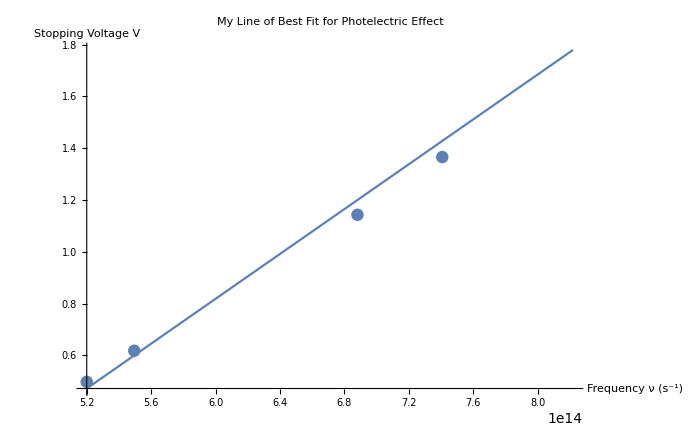

(2) The equation mathematica finds for the line of best fit is
	V(ν) = -1.77859+4.32906×10^-15 ν which directly matches my line of best of fit, and the plot is shown below:

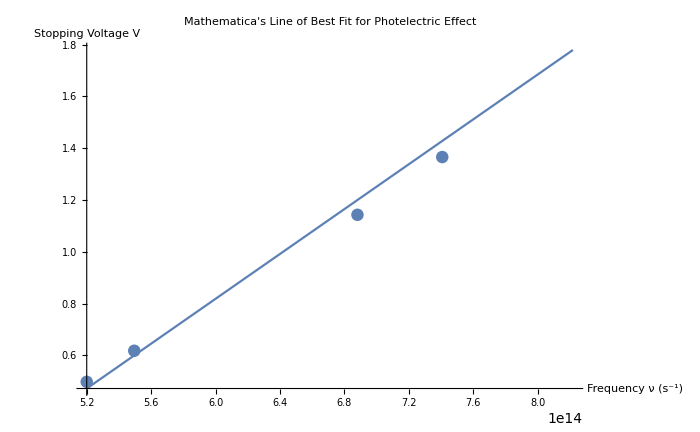

```mathematica
(*Fitting-M2*)
(*Jared Frazier*)
(*09-20-20*)
(*Description: 
First derive the line of best fit for a linear equation ŷ = Subscript[β, 0] + Subscript[β, 1] X, that is 
derive the coffecients Subscript[β, 0] and Subscript[β, 1]. Once these two coefficients are derived, use the following observations
from the Cathode Ray experiment to derive the variables associated with the equation modeling stopping 
voltage and frequency of light:

[1] The photoelectric effect is the emission of electrons when electromagnetic radiation (e.g., light),
hits a material.
[2] The expected emission of electrons was essentially continuous, meaning as the intensity (average power transfer over 
one period of the wave) of light increased, it was expected that the kinetic energy of emitted electrons would be
proportional. This expectation was refuted with experimental results.
[3] Incident light (radiation) had to have a frequency exceeding a certain threshold before electrons were ejected.
[4] The stopping potential V is the voltage at which no electrons that are emitted from the metal plate subject
to incident radiation are able to reach another plate (due to electron-electron repulsion). The stopping voltage
was measured for different frequencies ν of the incident beam.
[5] Lastly, it is observed from Einstein and the Cathode Ray Experiment that the kinetic energy of the ejected  electrons
must be Subscript[E, k] = hν - ϕ = hν - Subscript[hν, 0] where the units of Subscript[E, k] are the electron charge e and the voltage V. Solving for 
voltage, the stopping voltage becomes a simple linear equation whose parameters can be determined by minimzizing the 
sum of squared errors w.r.t Subscript[β, 0] and Subscript[β, 1] such that V(ν) = h/e ν - h/e Subscript[ν, 0] = Subscript[β, 1] ν + Subscript[β, 0].

Refs:
https://aklectures.com/lecture/photoelectric-effect-compton-effect-wave-particle-duality/stopping-voltage-and-work-function
https://en.wikipedia.org/wiki/Photoelectric_effect*)

Clear["Global`"]

(*Import Notation package and define symbols*)
<<Notation`
Clear["Global`*"];
Notation[Subscript[β̂, 0] ⟺ betaNaught]
Notation[Subscript[β̂, 1] ⟺ betaOne]
Notation[Subscript[Ŷ, k] ⟺ yHat]
Notation[Subscript[Y, k] ⟺ yData]
Notation[Subscript[X, k] ⟺ xData]
Notation[Subscript[Y, avg] ⟺ yBar]
Notation[Subscript[X, avg] ⟺ xBar]

(*Deriving the slope (Subscript[β̂, 0]) and intercept(Subscript[β̂, 1])*)
(*General form of linear regression equation, betaNaught and betaOne are unknown constants currently*)
yHat = betaNaught + betaOne * xData;

(*Define the general form for the sum of square errors*)
sse = Sum[(yData - yHat)^2, {k, 1, N}]; 
sseSummand = (yData - yHat)^2;

(*Display logic*)
Print["Part 1 - Derivation of slope 'a' ((β̂)_1) and intercept 'b' ((β̂)_0):"]
Print["(1) Linear relationship between stopping voltage and frequency of incident light
\tV(ν) = aν + b can be modeled with the same equation (Ŷ)_k = ", yHat, " where (Ŷ)_k is the
\tpredicted response variable (V(ν)) and X_k is the kth explanatory variable (ν)."]
Print["(2) The sum of squared errors, also known as the mean squared error, is
\tthe sum of the difference between all response values in the data set (Y_k) and 
\tpredicted response values ((Ŷ)_k) and is modeled by the equation SSE = ∑_(k = 1)^N (Y_k-(Ŷ)_k)^2 
\tfor the k^th term in a data set with N terms."]
Print["(3) Substituting the definition of (Ŷ)_k into SSE yields an equation which,
\tonce differentiated with respect to (β̂)_1 and (β̂)_0 and set equal to 0, may be solved
\tsimultaneously to yield the minimum values of (β̂)_1 and (β̂)_0 to minimize the 'distance' 
\tbetween the prediction 'line' and values of Y_k: SSE = ∑_(k = 1)^N (Y_k-((β̂)_0 + (β̂)_1X_k))^2"]
(*Differentiate with respect to Subscript[β̂, 0] and Subscript[β̂, 1], derivative of summation is sum of derivatives*)
summandDerivBetaNaught = D[sseSummand, {betaNaught, 1}];
summandDerivBetaOne = D[sseSummand, {betaOne, 1}];
Print["(4)  (∂SSE)/(∂SubscriptBox[OverscriptBox[β, ^], 0])∑_(k = 1)^N (Y_k-((β̂)_0 + (β̂)_1X_k))^2 = ∑_(k = 1)^N ", summandDerivBetaNaught, 
"\tand (∂SSE)/(∂SubscriptBox[OverscriptBox[β, ^], 1])∑_(k = 1)^N (Y_k-((β̂)_0 + (β̂)_1X_k))^2 = ∑_(k = 1)^N ", summandDerivBetaOne]

(*Solve partial derivative with respect to betaNaught ==  0*)
soln1 = Solve[{summandDerivBetaNaught==0}, {betaNaught}];
storeSoln1 = betaNaught/.soln1[[1]];

(*Summation of a constant*)
summationRule = Sum[betaNaught, {k, 1, N}];

(*Display solution for Subscript[B̂, 0] in terms of Subscript[B̂, 1]*)
Print["(5) The solution for ", summationRule, " = ", storeSoln1, " for N values in the  
\tdata is equivalent to (B̂)_0 = Ȳ - (B̂)_1X̄ where Ȳ and X̄ are the average of the X and 
\tY values in the data."]

(*Equivalent solution for Subscript[B̂, 0]*)
betaNaughtAvg = yBar - betaOne*xBar;

(*Solve for Subscript[B̂, 1] by substituting Subscript[B̂, 0] in terms of Subscript[B̂, 1] into (∂SSE)/(∂Subscript[β̂, 1])*)
betaOneDerivOneVarSummand = xData * (-betaNaughtAvg - betaOne*xData + yData);

(*Display new summation*)
Print["(6) Substituting (B̂)_0 in terms of (B̂)_1 into (∂SSE)/(∂SubscriptBox[OverscriptBox[β, ^], 1]), ∑_(k = 1)^N " betaOneDerivOneVarSummand, 
" which simplifies to ∑_(k = 1)^N ", FullSimplify[betaOneDerivOneVarSummand] ]
(*Self expand*)
Print["(7) Expanding the summation using summation rules,
\t∑_(k = 1)^N X_k(Y_k-Y_avg) - (B̂)_1∑_(k = 1)^N X_k(X_k-X_avg)=0. Mathematica cannot recognize that there are 
\ttwo variables Y_k and X_k in the simplified equation. It treats all of them as 
\tconstants and the syntax x[[k]] or y[[k]] cannot be used either to indicate 
\tthe k^th variable of a predefined list (requires actual data)."]
Print["(8) Therefore, (B̂)_1 = (∑_(k = 1)^N)/(∑_(k = 1)^N) and (B̂)_0 = ", betaNaughtAvg]
Print[]

(*Function to convert wavelength to frequency*)
toFrequency[wave_] := (3*10^8)/(wave*10^(-9));

(*x and y values in photoelectric data set*)
xList = {toFrequency[365], toFrequency[405], toFrequency[436], 
         toFrequency[546], toFrequency[577]}; 
yList = {1.855, 1.366, 1.143, 0.618, 0.498};
numEle = 5;

(*Use derived equations to calc linear equation *)
Print["Part 2 - Calculate slope and intercept of the equation for stopping voltage as a function of frequency V(ν):"]

(*Calculate averages of x and y lists*)
xAvg = Sum[xList[[i]], {i,1,numEle}]/numEle;
yAvg = Sum[yList[[i]], {i,1,numEle}]/numEle;
calcBetaOne = Sum[xList[[i]]*(yList[[i]]-yAvg), {i, 1, numEle}]/Sum[xList[[i]]*(xList[[i]]-xAvg), {i, 1, numEle}];
calcBetaNaught = yAvg-calcBetaOne*xAvg;

(*Line of best fit*)
linEq[ν_] := calcBetaNaught + calcBetaOne*ν;
Print["(1) My line of best fit is V̂(ν) = ", linEq[ν], " and Planck's constant
\th is ", calcBetaOne, " eV*s which is close to the actual value
\t4.1357 × 10^-15 eV*s. Therefore, %error is ", 100*(Abs[calcBetaOne-4.13157*10^(-15)]/(4.13157*10^(-15))), "%"]

(*Standard Deviation and Correlation coefficient r*)
sx = (Sum[(xList[[i]] - xAvg)^2, {i,1,numEle}]/(numEle-1))^(1/2);
sy = (Sum[(yList[[i]] - yAvg)^2, {i,1,numEle}]/(numEle-1))^(1/2);
r = 1/(numEle-1)*Sum[(xList[[i]] - xAvg)/sx*(yList[[i]]-yAvg)/sy, {i,1,numEle}];

(*Coefficient of determination*)
r2 = r^2;
Print["(2) The coefficient of determination R^2 = ", r2, " from R = 1/(N - 1)*∑_(k = 1)^N (X_k/S_x)(Y_k/S_y)"]

(*How well the line predicts values*)
eqError = Sqrt[Sum[(yList[[i]]-linEq[xList[[i]]])^2, {i, 1, numEle}]/(numEle-2)];
Print["(3) The error associated with predicted value V̂(ν) is modeled by the equation
\tS = √((∑_(k = 1)^N)/(N  -  2)) = ±", eqError, " Volts" ]

(*Plot data with my line of best fit*)
Print[]
xy2dList = {{toFrequency[365], 1.855},{ toFrequency[405], 1.366},{toFrequency[436],1.143 },
            {toFrequency[546], 0.618}, {toFrequency[577], 0.498}};
Print["Part 3 - Plot the data with my line of best fit and mathematicas line of best fit:"]
Print["(1) My line of best fit is V̂(ν) = ", linEq[ν], " and the plot is shown below:"]
Show[{Plot[linEq[x], {x,toFrequency[577],toFrequency[365]}, PlotLabel->"My Line of Best Fit for Photelectric Effect",
AxesLabel->{"Frequency ν (s^-1)", "Stopping Voltage V"}, ImageSize->700],  ListPlot[xy2dList]}]

(*Mathematica's line of best fit formula*)
mathematicaLinEq = LinearModelFit[xy2dList, ν, ν];
functionMathematicaLinEq[ν_] = Normal[mathematicaLinEq];
Print["(2) The equation mathematica finds for the line of best fit is
\tV(ν) = ", Normal[mathematicaLinEq], " which directly matches my line of best of fit, and the plot is shown below:"]
Show[{Plot[functionMathematicaLinEq[x], {x,toFrequency[577],toFrequency[365]}, PlotLabel->"Mathematica's Line of Best Fit for Photelectric Effect",
AxesLabel->{"Frequency ν (s^-1)", "Stopping Voltage V"}, ImageSize->700],  ListPlot[xy2dList]}]
```